# Mappa logistica

Cammelli Tonanti, ovvero Riccardo Cazzin e Francesco Tognetti

Università degli Studi di Padova

Le iterazioni della mappa logistica f_μ=μx(1-x), che dipende dal parametro positivo μ, costituiscono (a prima vista) una versione discreta della dinamica continua descritta dall’equazione logistica. A differenza di quest’ultima, però, la dinamica discreta della mappa logistica è enormemente complicata.

## Evoluzione di un’epidemia

Prima di affrontare il tema principale, vogliamo dare un’applicazione del modello logistico che ha guadagnato una certa rilevanza nell’attualità: esso, infatti, modellizza in modo abbastanza accurato la diffusione di un’epidemia. Supponendo di avere N_d infetti il giorno d, che ogni infetto incontri E suscettibili e che li contagi con probabilità p, la variazione giornaliera di contagi seguirebbe la legge

∆N_d=E p N_d

che, trasformata in equazione differenziale con E e p costanti, darebbe come soluzione una funzione esponenziale. Dato che, però, è impossibile che il numero di infetti cresca sempre, anche oltre la popolazione totale, occorre considerare altri parametri, il più importante dei quali è il numero di suscettibili S, visto che un infetto non può contagiare un altro infetto. Un’equazione più adeguata, quindi, è del tipo

∆N_d=k(1-N_d/S)N_d

che è equivalente a

N_(d+1)=N_d+k(1-N_d/S)N_d

N_(d+1)=(N_d(1+k S-N_d))/S

N_(d+1)=N_d[(k S+1)-N_d]/S

e quest’ultima è una mappa logistica.

Per mostrare che il modello logistico (eventualmente corretto in un modello con somma di due logistiche per l’effetto “martello-danza”) applicato all’epidemia in Italia, abbiamo creato un pacchetto che tratta e manipola i dati pubblicati dalla Protezione Civile.

```mathematica
ClearSystemCache[];
<<"https://raw.githubusercontent.com/ZinRicky/cammelli-tonanti/master/01_Esame/01_Bella/CovidItalia.wl"
```

Controlliamo innanzitutto l’ultimo giorno di cui sono presenti i dati. Di solito è il giorno stesso o quello prima.

```mathematica
CovidUltimaData
```

Si rimanda al pacchetto per tutti i comandi implementati; la funzionalità più interessante è confrontare le due modellizzazioni di tipo logistico coi dati grezzi di casi totali e nuovi positivi: i nuovi positivi, infatti, possono essere approssimati con la derivata del modello dei casi totali.

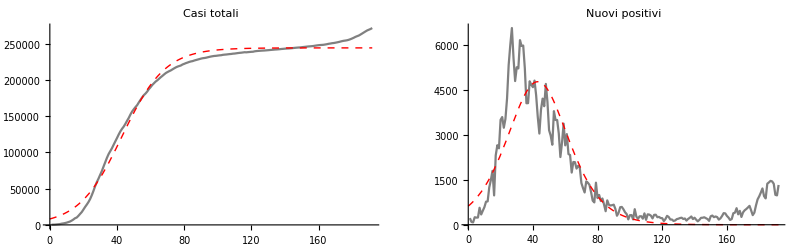

```mathematica
CovidItaliaPlot[1]
```

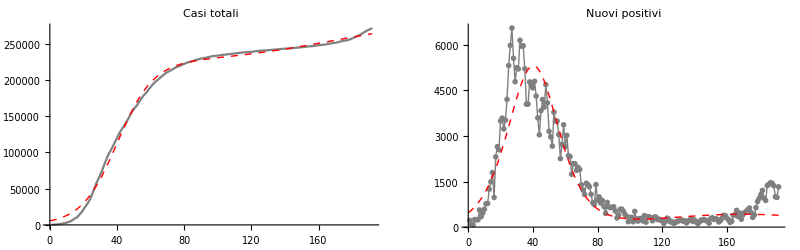

```mathematica
CovidItaliaPlot[2]
```

Come si può notare, il secondo modello è in generale più aderente del primo ai dati grezzi, perché prevede che dopo una prima stabilizzazione del numero di infetti ci sia un’altra piccola crescita, cosa che il modello logistico non prevede.

## Lemmi introduttivi e visualizzazione delle orbite.

Con mappa logistica intendiamo la funzione polinomiale reale f_μ(x)=μ x (1-x), con μ>0. Ci occuperemo soprattutto delle iterazioni di f_μ, ossia delle funzioni f_μ^n=f_μ∘…∘f_μ: studieremo, al variare del parametro μ, il comportamento delle orbite generate da f_μ, ovvero degli insiemi del tipo {x_0,f_μ(x_0),f_μ^2(x_0),…}; in particolare, vedremo sotto quali ipotesi tali orbite posseggano uno o più attrattori. In seguito, mostreremo un’applicazione, resasi assai attuale nell’ultimo periodo, che modellizza l’andamento di un’epidemia proprio con la mappa f_μ.

```mathematica
(*
Definiamo Subscript[f, μ].
Definiamo subito anche l'iterata di Subscript[f, μ], dato che la useremo molto spesso.
Per la versione non compilata, facciamo semplificare i radicali impliciti, così da poter lavorare facilmente anche con numeri esatti.
*)
f[μ_,x_]:=μ x(1-x)
fn[μ_,x_,n_]:=Nest[RootReduce[f[μ,#]]&,x,n] 
fnC=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[μ #(1-#)&,x,n]];
fnList[μ_,x_,n_]:=NestList[RootReduce[f[μ,#]]&,x,n]
fnCList=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},NestList[μ #(1-#)&,x,n]];
```

Applicando in modo iterato la mappa logistica a partire da un punto iniziale x_0∈ℝ, ci chiediamo se la mappa ammetta un punto fisso, ovvero un x_f_μ∈ℝ tale che f_μ(x_f_μ)=x_f_μ.

Lemma 1. Per ogni μ>0, f_μ ha come unici punti fissi 0 e 1-1/μ.

Dimostrazione. Si può lasciare a Mathematica la soluzione dell’equazione di punto fisso: si applica First per rimuovere le espressioni condizionali, dato che il caso μ=1 dà come unico punto fisso con molteplicità doppia il punto x=0. I punti trovati sono quelli richiesti dal Lemma.

```mathematica
First/@(x/.Solve[{μ>0,f[μ,x]==x},x,Reals])
```

□

A priori la mappa logistica potrebbe essere studiata su tutto ℝ. Coi prossimi lemmi, invece, mostriamo che lo studio più fecondo avviene nell’intervallo [0,1].

Lemma 2. Per ogni μ>1, se x_0>1 oppure x_0<0, allora f_μ^n(x_0)→-∞.

Dimostrazione. Mostriamo innanzitutto per quali x∈ℝ si abbia f_μ(x)<x. Se risulta che, chiamato U il sottoinsieme di ℝ che verifichi la disuguaglianza sopra, a tale U appartengono sia f_μ(x_0) sia x_0 per ogni x_0>1 e per ogni x_0<0, allora f_μ^n(x_0) è una successione monotona decrescente inferiormente illimitata, e si è provata la tesi.

```mathematica
Reduce[{μ>1,f[μ,x]<x},x,Reals]
```

È evidente, poi, che f_μ(x_0)<0 per ogni x_0>1>1-1/μ e per ogni x_0<0, dunque la successione f_μ^n(x_0) diverge a -∞ in questi due casi.

□

Lemma 3. Se x_0<0 oppure x_0>1, allora esiste 0<μ≤1 tale che f_μ^n(x_0)→-∞.

Dimostrazione. Usiamo un approccio analogo a quello del Lemma 2:

```mathematica
Reduce[{0<μ≤1,f[μ,x]<x},x,Reals]
```

Trattiamo innanzitutto il caso x_0>1:

```mathematica
Reduce[{0<μ≤1,x0>1,f[μ,x0]<(-1+μ)/μ},x0,Reals]
```

Scegliendo 1>μ>1/x_0>0 si ottiene quanto richiesto. Trattiamo ora il caso x_0<0: poiché è sufficiente che x_0<1-1/μ, basta scegliere 1>μ>1/(1-x_0)>0.

□

Col prossimo lemma, infine, restringiamo l’intervallo dei μ che intendiamo prendere in considerazione.

Lemma 4. Se 0<μ≤4, allora tutte le orbite con dato iniziale in [0,1] rimangono in tale intervallo. Se, invece, μ>4, allora esiste un intervallo A_0⊆[0,1] tale che ogni orbita con dato iniziale in A_0 non è contenuta in [0,1] a partire dalla prima iterazione.

Dimostrazione. La prova del Lemma 4 è immediata, se si considerano le seguenti disuguaglianze:

```mathematica
Reduce[{0≤x≤1,0≤f[μ,x]≤1,0<μ≤4},x]
Reduce[{0≤x≤1,0≤f[μ,x]≤1,μ>4},x]
```

□

Alla luce di questo risultato, decidiamo di studiare la dinamica della mappa logistica per μ<4.

Dopo aver delimitato quanto più possibile gli intervalli da studiare, osserviamo come può evolvere un'orbita al variare di μ e x_0.

```mathematica
graficoOrbita[μ_,x_,n_]:=With[
{
(*Precalcoliamo l'orbita, disposta sulla bisettrice.*)
pts=Table[{ξ,ξ},{ξ,fnCList[μ,x,n]}]
},
(*Disegniamo la parabola Subscript[f, μ] e la bisettrice del I e del III quadrante; mostriamo poi l'orbita tenendo traccia dell'ultimo punto (in azzurro).*)
Plot[
{f[μ,t],t},
{t,Min[x,0],Max[x,1]},

]
]
```

```mathematica
Manipulate[graficoOrbita[μ,x0,n],{{μ,1.2},0,4},{{x0,0.4},0,1},{{n,20},Range[10,150,10]}]
```

## Biforcazioni e caos

Grazie al grafico dinamico sopra, si può notare che per 0<μ≤1 tutte le orbite tendono a 0, unico punto fisso in [0,1] per tali μ. Ciò è dovuto al fatto che, con 0<μ≤1, si ha f_μ(x)≤x per ogni x∈[0,1], ma al contempo f_μ(x)≥0 per tali x in base al Lemma 4: per il teorema sul limite di successioni monotone, qualunque orbita con dato iniziale in [0,1] ammette limite e tale limite è proprio 0. La situazione cambia se μ>1.

Lemma 5. Per ogni μ>1 il punto 0 è un punto fisso repulsivo di f_μ.

Dimostrazione. Un punto fisso x_0 è repulsivo per f_μ se e solo se |f'_μ(x_0)|>1. Dal momento che f'_μ(0)=μ>1, la tesi è verificata.

```mathematica
D[f[μ,x],x]/.x->0
```

□

Per μ>1 il punto fisso x_μ=1-1/μ appartiene a [0,1] e, dunque, può essere preso in considerazione.

Lemma 6.  Il punto fisso x_μ=1-1/μ per f_μ è attrattivo per 1<μ<3 e repulsivo per μ>3.

Dimostrazione. Con un ragionamento simile a quello usato nel Lemma 5, calcoliamo la derivata di f_μ in x_μ:

```mathematica
Simplify[D[f[μ,x],x]/.x->1-1/μ]
```

Dato che |2-μ|<1 per 1<μ<3 e |2-μ|>1 per μ>3, si è provata la tesi.

□

Nel caso 1<μ≤3, dunque, le orbite di tutti gli x∈(0,1) convergono a x_μ e le orbite di 0 e 1 convergono a 0. Come si può notare a livello grafico, però, la convergenza verso x_μ diviene sempre più lenta man mano che μ si avvicina a 3 e, superatolo, essa scompare per lasciare il posto ad orbite di periodo 2.

Lemma 7. L’orbita di periodo minimo 2 di f_μ esiste per μ>3 ed è attrattiva per 3<μ<1+√6.

Dimostrazione. Se un’orbita per f_μ ha come periodo minimo 2, allora i due punti attrattivi x_1 e x_2 sono punti fissi di f_μ^2. Calcoliamo, dunque, i punti fissi di f_μ^2

```mathematica
Solve[{fn[μ,x,2]==x,μ>0,0≤x≤1},x,Reals]
```

Confrontando i quattro risultati ottenuti con i punti fissi di f_μ, spostiamo l’attenzione sugli ultimi due risultati, che valgono per μ>3. Calcoliamo la derivata di f_μ^2 nei punti fissi appena trovati:

```mathematica
Expand@FullSimplify[D[fn[μ,x,2],x]/.(Solve[{fn[μ,x,2]==x,μ>3},x,Reals]⟦{3,4}⟧/.ConditionalExpression[ξ_,_]->ξ)]
```

e vediamo per quali μ>3 sono punti attrattivi.

```mathematica
Reduce[RealAbs[#]<1&&μ>3,μ,Reals]&/@Expand@FullSimplify[D[fn[μ,x,2],x]/.(Solve[{fn[μ,x,2]==x,μ>3},x,Reals]⟦{3,4}⟧/.ConditionalExpression[ξ_,_]->ξ)]
```

Ciò conferma quanto affermato nella tesi.

□

Ogni nuova biforcazione è prodotta dallo stesso fenomeno analitico. Alla n-esima biforcazione, infatti, le orbite attrattive convergono ai punti fissi di f_μ^(2^n) che abbiano modulo della derivata strettamente minore di 1: posseggono questa caratteristica i punti fissi di f_μ^(2^n) che non sono anche punti fissi di f_μ^(2^(n-1)). Tali punti attrattivi compaiono non appena i punti fissi di f_μ^(2^n) che sono anche punti fissi di f_μ^(2^(n-1)) hanno derivata di modulo maggiore di 1; come si vede nel grafico sotto, infatti, la comparsa di nuovi attrattori è strettamente collegata al superamento della soglia 1 per il modulo della derivata calcolata negli attrattori “precedenti” — e questa crescita del modulo della derivata si ottiene con l’aumentare di μ.

```mathematica
Manipulate[
GraphicsRow[
{
Plot[{fn[μ,x,n],x},{x,0,1},
,
Epilog->{Red,Point[{x,x}]/.Solve[{fn[Rationalize@μ,x,n]==x,x≥0},x,Reals]}
],
Plot[{Abs[D[fn[μ,y,n],y]]/.y->x,1},{x,0,1},
,
Epilog->{Red,Point[{x,Abs[D[fn[μ,y,n],y]/.y->x]}]/.Solve[{fn[Rationalize@μ,x,n]==x,x≥0},x,Reals]}
]
}
],
{μ,3,3.57},
{n,2^Range[3]}
]
```

Dopo aver capito il motivo per il quale i punti perdono di attrattività dopo aver passato un certo μ, si può tracciare un grafico dei punti fissi e delle prime orbite attrattive al variare di μ: non vanno considerate in questo grafico le orbite non generate direttamente dalla biforcazione, perché di quelle non abbiamo dato spiegazione.

```mathematica
ListPlot[
Union@Flatten[
Table[
ParallelTable[{μ,x}/.NSolve[{fn[μ,x,n]==x,x≥0},x,Reals],{μ,Subdivide[0,4,10^3]}],
{n,2^Range[0,3]}
],
2
],

]
```

Questo grafico può essere “completato” registrando il comportamento dell’orbita di un singolo punto x_0 al variare di μ dopo un certo numero (alto) di iterazioni.

```mathematica
attrattivoData[n_,m_,{μ0_,μ1_,η_}]:=Union@Flatten[ParallelTable[,{μ,μ0,μ1,η}],1]
```

```mathematica
(*codaOrbita=attrattivoData[10^4,50,{0,4,10^-4}];*)(*Scegliamo di considerare al più le ultime 50 iterazioni calcolate per ogni μ*)
(*Se si vuole risparmiare tempo, è possibile importare codaOrbita già calcolato.*)
codaOrbita=Import["https://raw.githubusercontent.com/ZinRicky/cammelli-tonanti/master/01_Esame/03_Dati/C_completa.csv"];
```

```mathematica
Rasterize[ListPlot[codaOrbita,],ImageSize->1000]
```

Attraverso opportuni ingrandimenti, si nota che la struttura delle biforcazioni è in un certo senso autosimile: ogni nuova biforcazione mantiene una forma molto vicina alla precedente.

```mathematica
GraphicsGrid[Partition[MapThread[Rasterize[ListPlot[codaOrbita,],ImageSize->1000]&,],2],ImageSize->Full]
```

Quest’autosimilarità si ritrova non solo ad ogni biforcazione, ma anche nella parte di grafico in cui l’andamento delle orbite è meno regolare.

```mathematica
(*autoSimCaos=attrattivoData[10^4,100,{3.56,4,2 10^-5}];*)
autoSimCaos=Import["https://raw.githubusercontent.com/ZinRicky/cammelli-tonanti/master/01_Esame/03_Dati/C_caotica.csv"];
```

```mathematica
Rasterize[ListPlot[autoSimCaos,],ImageSize->1000]
```

Da tale ingrandimento si può intuire che gli intervalli “regolari” all’interno della regione dei μ “caotici” sono tanti e potenzialmente autosimili.

## Costante di Feigenbaum

Vogliamo capire se il susseguirsi delle biforcazioni a partire da μ=3 segua una certa regola specifica. Per fare ciò, ci occorrono innanzitutto i μ_n dopo i quali avviene una biforcazione; il metodo con cui li cerchiamo consta di due fasi:

una ricerca “grossolana” di un intervallo in cui l’attrattività passi dai punti fissi di f_μ^(2^n) a quelli di f_μ^(2^(n+1));

una ricerca “minuta” di una buona approssimazione del punto μ_n.

La prima fase di questa ricerca si basa sul seguente fatto: volendo cercare la n-esima biforcazione, scelto “un quasi qualunque” x_0∈(0,1), ovvero un x_0 che non risulti punto fisso di f_μ^M con M<2^n (e la scelta di x_0=0.4 ci garantisce di non incontrare una tale eventualità), la distanza tra f_μ^N(x_0) e f_μ^(N+2^n)(x_0) è infinitesima con l’aumentare di N. In particolare, se N è sufficientemente grande, la distanza tra i due stadi dell’orbita descritti prima è trascurabile.

Alla luce di ciò, fissiamo N∈ℕ abbastanza grande e registriamo quanti punti delle iterazioni di f_μ dalla N-esima alla (N+2^n')-esima sono “non trascurabilmente diversi”. Usiamo n'≥n, ove n∈ℕ indica la biforcazione che stiamo cercando: se usassimo solo direttamente n, gli errori numerici porterebbero a considerare μ molto più piccoli del necessario, come mostrerà l’esempio subito seguente l’implementazione; ciò comporterebbe un allungamento dei tempi di computazione — cosa che ovviamente vogliamo evitare. Per risparmiare ulteriore tempo di computazione, restringiamo la ricerca ad intervalli specifici, ovvero un intorno di 3 e l’intervallo [1+√6,3.57].

```mathematica
(*Definiamo la funzione con cui accomuniamo due punti dell'orbita se sono "abbastanza vicini".*)
conf[μ_,n_,Ν_]:=Length[Union[Round[10^4 Abs[fnC[μ,0.4,Ν+#]-fnC[μ,0.4,Ν]],1]&/@Range[2^n]]]
(*polishlastdata[n_,error_,ddata_]:=First@Last@Cases[FixedPoint[
If[Last@Last@Cases[ddata,{_,2^n}]==Last@#⟦Length[Cases[ddata,{_,2^n}]]-error⟧&@Cases[ddata,{_,2^n}],ddata,Drop[ddata,-1]],ddata],{_,2^n}]*)
```

```mathematica
(*deviazioni=Flatten[ParallelTable[{μ,conf[μ,#⟦1⟧,#⟦2⟧]},{μ,#⟦3⟧,#⟦4⟧,10^(-#⟦5⟧)}]&/@{{2,300,2.95,3.05,5},{4,600,3.35,3.5,5},{5,1000,3.5,3.57,6},{6,5000,3.564,3.57,6},{7,10000,3.568,3.57,7}},1];*)
deviazioni=Import["https://raw.githubusercontent.com/ZinRicky/cammelli-tonanti/master/01_Esame/03_Dati/D_deviazioni.csv"];
```

```mathematica
Rasterize[ListPlot[deviazioni,]]
```

Il grafico mostra che la convergenza verso gli attrattori si fa sempre più lenta in prossimità dei punti di biforcazione, fino a quando essi perdono di attrattività e il periodo raddoppia. Individuati, dunque, gli intervalli nei quali avviene questo fenomeno, cerchiamo per quali punti in particolare la differenza tra f_μ^N(x_0) e f_μ^(N+2^n)(x_0) è più alta a causa degli errori numerici: quelli saranno, con buona approssimazione, i punti di biforcazione.

```mathematica
(*Teniamo conto della distanza tra fn[μ, Subscript[x, 0], N] e fn[μ, Subscript[x, 0], N + 2^n] e selezioniamo come punto di biforcazione quello in cui tale distanza (che presumiamo non nulla) è massima.*)
dist[μ_,x0_,Ν_,n_]:=Abs[fnC[μ,x0,Ν]-fnC[μ,x0,Ν+2^n]]
indagine[n_,x0_,Ν_,{min_,max_,step_}]:=ParallelTable[{μ,dist[μ,x0,Ν,n]},{μ,min,max,step}]
indaginePlot[n_,x0_,Ν_,{min_,max_,step_}]:=ListPlot[indagine[n,x0,Ν,{min,max,step}],]
sospetto[n_,x0_,Ν_,{min_,max_,step_}]:=Module[
{
ind=indagine[n,x0,Ν,{min,max,step}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
colpevole[n_,x0_,Ν_,{min_,max_,step_}]:=sospetto[n,x0,Ν,{min,max,step}]⟦1,1⟧
```

Qui di seguito mostriamo gli intorni dei primi otto punti di biforcazione con relativi errori numerici di convergenza.

```mathematica
With[
{
mostra=indaginePlot@@@{
{1,0.4,10^4,{2.99,3.01,10^-4}},
{2,0.4,10^4,{3.449,3.45,10^-5}},
{3,0.4,10^5,{3.543,3.545,10^-5}},
{4,0.4,10^5,{3.56435,3.5645,10^-6}},
{5,0.4,10^5,{3.56875,3.56877,10^-7}},
{6,0.4,10^5,{3.569685,3.5697,10^-7}},
{7,0.4,10^5,{3.56989,3.569895,10^-8}},
{8,0.4,10^5,{3.56993,3.56994,10^-8}}
}
},
Manipulate[mostra⟦n⟧,{{n,1,TraditionalForm["n_μ"]},Range[8]}]
]
```

Conoscendo esplicitamente i valori di μ_1 e μ_2, non è necessario ricercarli con il metodo sopra: li includiamo a parte per essere sicuri di non commettere errori numerici importanti.

```mathematica
biforcazioni=Join[
{3.,1.+√6},
colpevole@@@{
{3,0.4,10^5,{3.543,3.545,10^-5}},
{4,0.4,10^5,{3.56435,3.5645,10^-6}},
{5,0.4,10^5,{3.56875,3.56877,10^-7}},
{6,0.4,10^5,{3.569685,3.5697,10^-7}},
{7,0.4,10^5,{3.56989,3.569895,10^-8}},
{8,0.4,10^5,{3.56993,3.56994,10^-8}}
}
]
```

Assumendo l’asintotica (μ_(n+1)-μ_n)/(μ_n-μ_(n-1))~ϕ, proviamo a stimare un tale ϕ, detto costante di Feigenbaum, a partire dalle biforcazioni che abbiamo raccolte. Abbiamo deciso di escludere l’ultima biforcazione trovata per evitare errori relativi, più probabili per le biforcazioni successive.

```mathematica
rapporti=Table[(biforcazioni⟦n⟧-biforcazioni⟦n-1⟧)/(biforcazioni⟦n+1⟧-biforcazioni⟦n⟧),{n,2,6}];
ϕ=Last[rapporti];
```

Dalla formula sopra si ricava che μ_(n+1)~(μ_n-μ_(n-1))ϕ+μ_n: in questo modo si può dare una stima di μ_∞.

```mathematica
nuovaBiforcazione[n_Integer]:=nuovaBiforcazione[n]=Piecewise[{{biforcazioni[[n]], n≤8}, {(nuovaBiforcazione[n-1]-nuovaBiforcazione[n-2])/ϕ+nuovaBiforcazione[n-1], n>8}}]
```

```mathematica
NumberForm[nuovaBiforcazione@50,16]
```

Questo stesso fatto può essere usato anche per ricavare una formula asintotica per le biforcazioni μ_n: trovati μ_1 e μ_2, infatti, si vede che

μ_3~((ϕ+1)μ_2-μ_1)/ϕ

μ_4~((ϕ+1)μ_3-μ_2)/ϕ=((ϕ^2+ϕ+1)μ_2-(ϕ+1)μ_1)/ϕ^2

e, per induzione, si può mostrare che

μ_n~(μ_2∑_(i=0)^(n-1) ϕ^i-μ_1∑_(i=0)^(n-2) ϕ^i)/ϕ^(n-1)=(μ_2(1-ϕ^(n-1))/(1-ϕ)-μ_1(1-ϕ^(n-2))/(1-ϕ))/ϕ^(n-1)

Questa formula non può essere usata per ricavare direttamente le biforcazioni sia perché gli errori nella stima della costante ϕ condizionano pesantemente i risultati sia perché la relazione con ~ non è un’uguaglianza. Provando, infatti, ad utilizzare la stima per μ_n con n alto, si nota che questa stima non ha affatto una precisione utile all’indagine numerica.

## Universalità della costante di Feigenbaum

La costante di Feigenbaum non è propria della sola funzione logistica, ma di qualunque mappa iterata continua [0,1]→[0,1] nulla agli estremi, non negativa altrove e con un unico massimo. Prendiamo in esame la funzione g_μ(x)=μ sin(π x).

```mathematica
g=Compile[{{μ,_Real},{x,_Real}},μ Sin[π x]];
gn=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[g[μ,#]&,x,n]];
gnList=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},NestList[g[μ,#]&,x,n]];
```

```mathematica
graficoOrbita2[μ_,x_,n_]:=With[
{
pts=Table[{ξ,ξ},{ξ,gnList[μ,x,n]}]
},
Plot[
{g[μ,t],t},
{t,Min[x,0],Max[x,1]},

]
]
```

```mathematica
Manipulate[graficoOrbita2[μ,x0,n],{{μ,0.5},0,1},{{x0,0.3},0,1},{{n,20},Range[10,150,10]}]
```

Le dinamiche che possiamo vedere nel grafico delle orbite richiamano subito quanto visto per la mappa logistica. Simile alla logistica è anche il diagramma delle biforcazioni.

```mathematica
(*codaOrbitaSin=Union@Flatten[ParallelTable[Take[NestList[Chop[g[μ,#]]&,0.3,10^5],-50]/.ξ_?NumericQ->{μ,ξ},{μ,0.,1,10^-5}],1];*)
codaOrbitaSin=Import["https://raw.githubusercontent.com/ZinRicky/cammelli-tonanti/master/01_Esame/03_Dati/D_universale.csv"];
```

```mathematica
Show[Rasterize[ListPlot[codaOrbitaSin,],ImageSize->1500],ImageSize->Full]
```

La deformazione dell’asse x enfatizza la somiglianza al caso della mappa logistica.

Ricerchiamo ora le biforcazioni e calcoliamone i rapporti che stimano ϕ.

```mathematica
dist2[μ_,x0_,Ν_,n_]:=Abs[gn[μ,x0,Ν]-gn[μ,x0,Ν+2^n]]
indagine2[n_,x0_,Ν_,{min_,max_,step_}]:=ParallelTable[{μ,dist2[μ,x0,Ν,n]},{μ,min,max,step}]
indagine2Plot[n_,x0_,Ν_,{min_,max_,step_}]:=ListPlot[indagine2[n,x0,Ν,{min,max,step}],]
sospetto2[n_,x0_,Ν_,{min_,max_,step_}]:=Module[
{
ind=indagine2[n,x0,Ν,{min,max,step}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
colpevole2[n_,x0_,Ν_,{min_,max_,step_}]:=sospetto2[n,x0,Ν,{min,max,step}]⟦1,1⟧
```

```mathematica
With[
{
mostra=indagine2Plot@@@{
{1,0.3,10^4,{0.316,0.32,10^-5}},
{2,0.3,10^5,{0.7196,0.7202,10^-6}},
{3,0.3,10^5,{0.8332,0.83335,10^-6}},
{4,0.3,10^5,{0.8584,0.8588,10^-6}},
{5,0.3,10^5,{0.86405,0.8641,10^-7}},
{6,0.3,10^6,{0.8652585,0.8652595,10^-9}},
{7,0.3,10^6,{0.8655105,0.86551085,10^-9}}
}
},
Manipulate[mostra⟦n⟧,{{n,1,TraditionalForm["n_μ"]},Range[7]}]
]
```

```mathematica
biforcazioni2=colpevole2@@@{
{1,0.3,10^4,{0.316,0.32,10^-5}},
{2,0.3,10^5,{0.7196,0.7202,10^-6}},
{3,0.3,10^5,{0.8332,0.83335,10^-6}},
{4,0.3,10^5,{0.8584,0.8588,10^-6}},
{5,0.3,10^5,{0.86405,0.8641,10^-7}},
{6,0.3,10^6,{0.8652585,0.8652595,10^-9}},
{7,0.3,10^6,{0.8655105,0.86551085,10^-9}}
}
```

```mathematica
rapporti2=Table[(biforcazioni2⟦n⟧-biforcazioni2⟦n-1⟧)/(biforcazioni2⟦n+1⟧-biforcazioni2⟦n⟧),{n,2,6}]
```

Si può intuire che la successione dei rapporti converga anche in questo caso allo stesso ϕ trovato per la mappa logistica.

## Oltre μ_∞: dinamiche caotiche

Finora ci siamo occupati soprattutto di studiare il comportamento di f_μ per μ<μ_∞, trattando dei raddoppiamenti del periodo che si incontrano a partire da μ_1=3. Se, invece, μ≥μ_∞, le dinamiche del sistema possono essere di due tipi:

dinamiche regolari, che saranno trattate nella prossima sezione;

dinamiche caotiche.

Con dinamiche caotiche intendiamo le dinamiche tali che piccoli cambiamenti di x_0 generano variazioni non trascurabili nelle code delle orbite — in realtà già a partire da un certo N∈ℕ non troppo grande. Nel grafico sottostante mostriamo i due tipi di dinamiche a confronto per variazioni dell’ordine di 10^-15.

```mathematica
GraphicsRow[
{ListPlot[{fnList[3.836,0.4,200],fnList[3.836,0.4+2$MachineEpsilon,200]},],ListPlot[{fnList[3.7,0.4,200],fnList[3.7,0.4+2$MachineEpsilon,200]},]},
ImageSize->Full
]
```

Come si può notare nel grafico a destra, la dinamica caotica si traduce in uno sfasamento pronunciato tra due orbite con dato iniziale molto vicino. Ancor più interessante è il grafico degli “errori assoluti” del tipo |f_μ^N(x_0)-f_μ^N((x̄)_0)|.

```mathematica
differenze[μ_,x0_,δ_,Ν_]:=RealAbs[fnCList[μ,x0,Ν]-fnCList[μ,x0+δ,Ν]]
```

```mathematica
GraphicsGrid[
Partition[
Table[
Rasterize[
ListPlot[differenze[μ,0.4,2$MachineEpsilon,200],],
ImageSize->500
],
{μ,Subdivide[3,4,7]}
],
2],
ImageSize->Full
]
```

Per μ<μ_∞ si ha il risultato prevedibile che orbite con dato iniziale molto vicino sono definitivamente molto vicine — e in realtà convergono verso gli stessi attrattori. Per la maggior parte dei μ>μ_∞, invece, si nota che, oltre una certa iterazione, le due orbite si separano in maniera non trascurabile, fino al punto di differire in modo sensibile. Come mostrato sopra, esistono anche dei μ>μ_∞ tali da ammettere orbite attrattive. Per capire quale sia la ratio con cui le orbite si separano, è utile un grafico logaritmico di due orbite con μ distinti.

```mathematica
GraphicsRow[
{ListLogPlot[differenze[3.835,0.4,2$MachineEpsilon,200],],ListLogPlot[differenze[3.7,0.4,2$MachineEpsilon,200],]},
ImageSize->Full
]
```

Il grafico di destra mostra molto chiaramente che la separazione delle orbite è inizialmente paragonabile ad un’esponenziale, mentre in seguito è limitata superiormente per via del Lemma 4. Questo fenomeno si può spiegare con la stima dell’errore tramite gli esponenti di Lyapunov, che vedremo in seguito. Studiamo innanzitutto come si comportano gli errori assoluti in funzione di μ: ci concentriamo soprattutto sui μ>μ_∞, per i quali sono possibili dinamiche caotiche.

```mathematica
stima[μ_,x0_,δ_,Ν_]:=Log[differenze[μ,x0,δ,Ν]]/.Indeterminate->0
studioStima[list_]:={#⟦1⟧,D[Normal[LinearModelFit[{Range[0,Length[#⟦2⟧]-1],#⟦2⟧}ᵀ,x,x]], x]}&/@list
```

```mathematica
variaμ=Table[{μ,stima[μ,0.4,2$MachineEpsilon,120]},{μ,3.57,4,10^-4}];
```

```mathematica
Show[Rasterize[ListPlot[studioStima[variaμ],],ImageSize->800],ImageSize->Scaled[0.6]]
```

Il grafico mostra un certo andamento generale degli errori assoluti, i quali tendono a crescere esponenzialmente fino al loro limite “naturale”. C’è da notare, però, che per alcuni μ ciò non è vero, e che anzi si registra una decrescita della distanza tra le orbite vicine: ciò si spiega col fatto che per quei μ la dinamica non è caotica, ma regolare, perché esistono n∈ℕ e alcuni x_i∈(0,1) tali che f_μ^n abbia in questi x_i derivata in modulo minore di 1. Mostriamo che per questi μ la dinamica è proprio regolare.

```mathematica
variaμcampione=Table[{μ,stima[μ,0.4,2$MachineEpsilon,120]},{μ,3.57,4,10^-3}];(*Decidiamo di estrarre un campione dai dati precedenti per poterli mostrare tutti graficamente.*)
```

```mathematica
GraphicsGrid[
Partition[Rasterize[ListPlot[fnList[#,0.4,100],],ImageSize->Medium]&/@First/@Cases[studioStima@variaμcampione,{_,a_}/;a≤0],4],ImageSize->Full
]
```

Per calcolare gli espoenenti di Lyapunov al variare di μ è sufficiente manipolare il logaritmo degli errori assoluti usato in precedenza: dato che λ~(log|f_μ^N(x_0)-f_μ^N(x_0+δ)|)/(N log|δ|), è sufficiente controllare se (log|f_μ^N(x_0)-f_μ^N(x_0+δ)|)/(N log|δ|) si annulla (per la precisione di macchina) in un tempo N finito oppure se si assesta attorno un valore positivo.

```mathematica
stimaLyapunov[μ_,x0_,δ_,Ν_]:=Module[{list=stima[μ,x0,δ,Ν]},(Drop[list,1]-Log[Abs@δ])/Range[Ν]]
```

È interessante notare che, per com’è costruito il programma, μ_∞ sarebbe l’estremo inferiore dei μ per cui stimaLyapunov(μ,x_0,δ,n)→ℓ>0 per n→∞, in quanto il programma restituisce Indeterminate per le orbite molto vicine.

```mathematica
First@Cases[{#,stimaLyapunov[#,0.6,2$MachineEpsilon,8000]//Last}&/@Range[3.569,3.57,10^-6],{_,_Real}]
```

Se, poi, si osserva il grafico della stima dell’esponente di Lyapunov in funzione di μ, si notano proprio le finestre regolari già viste con gli errori assoluti.

```mathematica
Show[Rasterize[ListPlot[Table[{μ,stimaLyapunov[μ,0.6,2$MachineEpsilon,2000]//Last},{μ,3.57,4,10^-4}],],ImageSize->1000],ImageSize->Scaled[0.66]]
```

## Oltre μ_∞: finestre regolari

Come già accennato sopra, esistono alcuni μ>μ_∞ che non determinano un comportamento caotico delle orbite della mappa logistica. Una particolarità di alcuni di questi μ è la formazione di orbtie attrattive di periodo 3, cosa che in un primo momento potrebbbe essere considerata completamente slegata dalle dinamiche dei μ<μ_∞. Quest’ultima sezione mostra che, invece, l’esistenza di un’orbita di periodo 3 implica l’esistenza di orbite di qualunque altro periodo.

Definiamo innanzitutto una relazione di ordine totale sui numeri naturali nel modo seguente:

| 3 | → | 5 | → | 7 | → | 9 | → | 11 | → | …
→ | 3·2 | → | 5·2 | → | 7·2 | → | 9·2 | → | 11·2 | → | …
→ | 3·2^2 | → | 5·2^2 | → | 7·2^2 | → | 9·2^2 | → | 11·2^2 | → | …
→ | 3·2^n | → | 5·2^n | → | 7·2^n | → | 9·2^n | → | 11·2^n | → | …
→ | 2^5 | → | 2^4 | → | 2^3 | → | 2^2 | → | 2 | → | 1

Quest’ordine ha 3 come supremo e 1 come infimo. Il nostro obiettivo è dimostrare che, se m→n e f_μ ha un’orbita attrattiva di periodo m, allora ne ha anche una di periodo n. Occorrono innanzitutto i seguenti lemmi.

Lemma 8 (Teorema del punto fisso di Brouwer). Sia f∶I→ℝ una funzione continua, ove I⊆ℝ è intervallo. Se f(I)⊆I, allora f ha un punto fisso in I.

Lemma 9. Sia f∶I→ℝ una funzione continua, ove I⊆ℝ è intervallo. Dato U⊆I, se V⊆f(U), allora esiste U_0⊆U tale che V=f(U_0).

Ora possiamo enunciare e dimostrare il teorema nel caso della mappa logistica.

Teorema di Шарко́вський. Sia f∶I→I una funzione continua. Se f ha un punto periodico primitivo di periodo m, allora per ogni n tale che m→n f possiede un punto periodico di ordine n.

Dimostrazione. Verifichiamo innanzitutto che la mappa logistica soddisfi alle condizioni delle ipotesi del Lemma 8: troviamo il massimo di f_μ.

```mathematica
f[μ,x/.Solve[D[f[μ,x], x]==0,x]⟦1⟧]
```

Abbiamo, dunque, che f_μ(ℝ)=(-∞,μ/4]⊆ℝ ed è continua: per il Lemma 8, quindi, f_μ ammette un punto fisso per ogni μ. Per rendere più facile lo svolgimento della dimostrazione, sfruttiamo il codice per la ricerca grossolana del periodo delle orbite attrattive e cerchiamo una finestra regolare di periodo 3.

```mathematica
Show[Rasterize[ListPlot[ParallelTable[{μ,conf[μ,2,3000]},{μ,3.82,3.85,10^-6}],],ImageSize->1000],ImageSize->Full]
```

Come si può evincere dal grafico, scegliere μ=3.835 garantisce che esista un’orbita attrattiva di periodo 3; per il resto della dimostrazione assumeremo che μ abbia tale valore.

```mathematica
f3[x_]:=f[3835/1000,x]
fn3[x_,n_]:=fn[3835/1000,x,n]
fn3List[x_,n_]:=fnList[3835/1000,x,n]
```

Chiamiamo 𝔞,𝔟,𝔠 gli attrattori dell’orbita per μ:

```mathematica
{𝔞,𝔟,𝔠}=fn3[0.5,#]&/@{80,81,82}(*Questo numero di iterazioni è sufficiente per stabilizzare l'orbita.*)
```

Definiamo, poi, due intervalli I_0=[𝔞,𝔟] e I_1=[𝔟,𝔠], che hanno come estremi proprio i tre punti trovati sopra. Vogliamo mostrare, ora, che f_μ ammette un punto fisso, ovvero un’orbita di periodo 1 — cosa che in realtà abbiamo già mostrato nel Lemma 1: dato che f_μ(𝔞)=𝔟, f_μ(𝔟)=𝔠 e f_μ(𝔠)=𝔞, si ha che [𝔞,𝔠]⊆f_μ(I_1); per il Lemma 8 esiste un punto fisso nell’interno di I_1. Sappiamo già che il punto fisso di f_μ è x_μ=1-1/μ, e una rapida verifica permette di verificare che è proprio in I_1.

```mathematica
ℐ1=Interval[{𝔟,𝔠}];
RegionMember[ℐ1,{1-1/3.835}]
```

Mostriamo ora che f_μ ammette un’orbita di periodo 5.

```mathematica
𝒶=First[α/.FindInstance[{f3[α]==β,f3[β]==γ,f3[γ]==δ,f3[δ]==ϵ,f3[ϵ]==α,α≠0,β≠0,γ≠0,δ≠0,ϵ≠0},{α,β,γ,δ,ϵ},Reals]];
```

```mathematica
ListPlot[fn3List[𝒶,150],]
```

A livello teorico, ciò si giustifica con il Lemma dell’itinerario, che mostreremo più nel dettaglio in seguito: se esistono intervalli J_1,…,J_5 tali che f_μ(J_1)⊇J_2, …,f_μ(J_4)⊇J_5 e f_μ(J_5)⊇J_1, allora esiste un punto x che tramite f_μ cicla tra questi intervalli tale che f_μ^5(x)=x, ovvero che abbia periodo 5 (in particolare non ha periodo 3). La dimostrazione di questo lemma, però, non è costruttiva — il che rende difficile trovare tali intervalli in modo esplicito. Per dare comunque una controparte grafica a questo lemma, abbiamo creato delle approssimazioni di tali intervalli a partire dai punti di periodo 5 trovati; si parla di approssimazioni proprio perché alcuni intervalli sono molto piccoli, al punto di renderli visivamente insignificanti: alla quarta iterazione, in particolare, non si trova un intervallo sufficientemente grande appropriato.

```mathematica
𝒥={#-0.025,#+0.025}&/@fn3List[𝒶,4];
fJ=RotateRight[f3[#] & /@𝒥];
Show[ListPlot[{{#,𝒥⟦#,1⟧},{#,𝒥⟦#,2⟧}}&/@Range[5], PlotStyle->Green],ListPlot[{{#,fJ⟦#,1⟧},{#,fJ⟦#,2⟧}}&/@Range[5], PlotStyle->Red]]
```

Dopo aver risolto questi casi più “facili”, passiamo alla dimostrazione del Teorema vero e proprio. Essa consta di tre parti:

se f_μ ammette un punto che genera un’orbita di periodo n>2, allora f_μ possiede un’orbita di periodo 2;

se f_μ ammette un punto che genera un’orbita di periodo dispari m≥3, allora f_μ possiede un’orbita di periodo n per ogni n≥m+1;

se f_μ ammette un punto che genera un’orbita di periodo dispari m≥3, allora f_μ possiede un’orbita di periodo n per ogni n pari.

Mostriamo il primo punto. Siano innanzitutto k,m,n,s∈ℕ. Supponiamo che y_0∈[0,1] generi una m-orbita tramite f_μ: per la struttura ciclica di {f_μ^k(y_0)∶k≤n}≃C_n, y_0 è un punto periodico di f_μ^n di periodo m/(MCD(m,n)); per lo stesso motivo, se y_1∈[0,1] è punto periodico di f_μ di periodo k, allora è punto periodico di periodo (k n)/s, ove s|n e MCD(s,k)=1.

Siano ora, invece, c,d∈[0,1] tali che f_μ(d)≤c<d≤f_μ(c): mostriamo che f_μ ha un punto periodico di periodo 2. Definiamo w=min{x∈[c,d]∶f_μ(x)=x} e v∈[0,1] tale che f_μ(v)=d: in base a quest’ultima definizione, f_μ^2(v)=f_μ(d)≤c<d. Dato che f_μ(0)=0, definiamo anche t=max{x∈[0,c]∶f_μ(x)=x}, cosicché f_μ non abbia punti fissi in (t,v], e u∈[t,c] tale che f_μ(u)=c: dal momento che f_μ^2(u)=f_μ(c)≥d≥u, segue che {f_μ^2(u)≥u
f_μ^2(v)≤v e, per il Teorema di Weierstrass, esiste y∈[u,v] tale che f_μ^2(y)=y. Poiché, però, f_μ non ha punti fissi in [u,v], y è un punto di periodo 2 per f_μ — in particolare non è un punto fisso di f_μ.

Consideriamo ora una m-orbita P={x_i∶i=1,…,m} di f_μ, ove x_i<x_j se e solo se i<j. Dal momento che x_1<f_μ(x_1) e f_μ(x_m)<x_m, esiste s∈ℕ tale che 1≤s≤m-1 e x_s=max{x∈P∶x<f_μ(x)}. Da ciò si conclude che f_μ(x_(s+1))≤x_s<x_(s+1)≤f_μ(x_(s+1)) e, per quanto visto nel paragrafo precedente, si è provato il primo punto.

Questo punto, nel caso della logistica, risulta evidente per μ_1<μ<μ_2, ma può essere osservato facilmente anche nel caso in esame in questo momento.

```mathematica
FindInstance[{α≠0,β≠0,f3[α]==β,f3[β]==α},{α,β},Reals]//N
```

Mostriamo ora gli ultimi due punti; la dimostrazione è il Lemma dell’itinerario accennato sopra: occorre mostrare che, se esistono intervalli J_1,…,J_m tali che J_(i+1)⊆f_μ(J_i) e che J_1⊆f_μ(J_m) e f_μ ha un’orbita di periodo dispari m≥3, allora ha orbite di ogni periodo dispari maggiore di m e di ogni periodo pari. Sia, dunque, x_1∈[0,1] un punto di periodo m: esso, dunque, ha orbita {x_1,…,x_m}. Per com’è fatta quest’orbita, esiste p∈J_m di periodo m per il Lemma 8; si ha p≠x_(n-1), perché altrimenti f_μ(p)=f_μ(x_(n-1))=